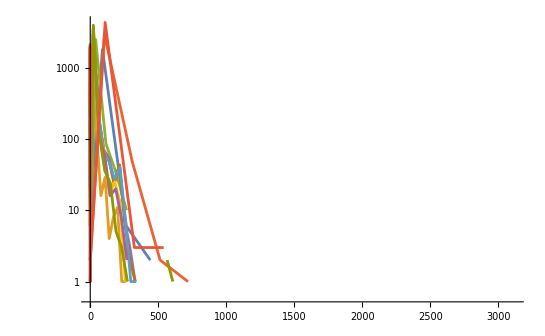

```mathematica
file=FileNameJoin[{NotebookDirectory[],"output_line4.json"}];
data=Import[file];
data[[;;,1]];

maxN=100;

(*Bar Chart Plot*)
Manipulate[n=ToString[m];
BarChart[("size"<>n)/. data,ChartLabels->("mid_interval"<>n)/. data],{m,0,maxN,10}]

(*Logarithmic ListPlot*)
ListLogPlot[Table[n=ToString[m];
Transpose@{("mid_interval"<>n)/. data,("size"<>n)/. data},{m,0,maxN,10}],Joined->True,PlotRange->Full]
```

```mathematica
MyVectorAngle[u_,v_]:=Module[{nu,nv},
nu=Norm[u];
nv=Norm[v];
Return[2*ArcTan[Norm[nv*u-nu*v]/Norm[nv*u+nu*v]]]
];
a={1,-1,2};
b={0,1,1};
N@MyVectorAngle[a,b]
N@VectorAngle[a,b]
```

1.27795

1.27795

```mathematica
a={A0,A1,A2};
b={B0,B1,B2};
c={C0,C1,C2};
V={v0,v1,v2};


a={0,0,0};
b={B0,B1,B2};
c={C0,C1,C2};
V={v0,v1,v2};

A=a+V;
N0=Cross[b-a,c-a]
N1=Cross[b-A,c-A]
FullSimplify[Dot[N0,N1]/FullSimplify[RootMeanSquare[N0]*Sqrt[3]*RootMeanSquare[N1]*Sqrt[3]]]
```

{-B2 C1+B1 C2,B2 C0-B0 C2,-B1 C0+B0 C1}

```mathematica
FullSimplify[RootMeanSquare[N0]*Sqrt[3]*RootMeanSquare[N1]*Sqrt[3]]
```

√((B1 C0-B0 C1)^2+(B2 C0-B0 C2)^2+(B2 C1-B1 C2)^2) √((B1 C0-B0 C1-B1 v0+C1 v0+B0 v1-C0 v1)^2+(B2 C0-B0 C2-B2 v0+C2 v0+B0 v2-C0 v2)^2+(B2 C1-B1 C2-B2 v1+C2 v1+B1 v2-C1 v2)^2)

```mathematica
A=V;
N0=Cross[b,c]
N1=Cross[b-V,c-V]
FullSimplify[FullSimplify[Dot[N0,N1]]/FullSimplify[RootMeanSquare[N0]*Sqrt[3]*RootMeanSquare[N1]*Sqrt[3]]]
```

```mathematica
FullSimplify[Dot[N0,N1]]
```

(B1 C0-B0 C1) (B1 (C0-v0)+C1 v0-C0 v1+B0 (-C1+v1))+(B2 C0-B0 C2) (B2 (C0-v0)+C2 v0-C0 v2+B0 (-C2+v2))+(B2 C1-B1 C2) (B2 (C1-v1)+C2 v1-C1 v2+B1 (-C2+v2))

```mathematica
isFlat[a_,b_,limRad_]:=Dot[a,b]>Cos[limRad]*Norm[a]*Norm[b]
```

```mathematica
isFlat[a_,b_,limRad_]:=Dot[a,b]>Cos[limRad]*Norm[a]*Norm[b]
MyVectorAngle[a_,b_]:=Module[{na,nb},
na=Norm[a];
nb=Norm[b];
Return[2*ArcTan[Norm[nb a+na b],Norm[nb a-na b]]]]



Manipulate[
(*Define your vectors*)
a={Cos[θ1],2Sin[θ1]};
b={2Cos[θ2],Sin[θ2]};
limRad=Pi/10; (*Example limit in radians*)
(*Create the plot*)
Graphics[{{Blue,Arrow[{{0,0},a}]},
{Red,Arrow[{{0,0},b}]},
{Black,Text[If[isFlat[a,b,limRad],{"Flat",Dot[a,b],Cos[limRad]*Norm[a]*Norm[b],VectorAngle[a,b]-MyVectorAngle[a,b]},{"Not Flat",Dot[a,b],Cos[limRad]*Norm[a]*Norm[b],VectorAngle[a,b]-MyVectorAngle[a,b]}],{3,3}]}}
,Axes->True,AxesLabel->{"x","y"}
,PlotRange->{{-5,5},{-5,5}}]
,{θ1,0,2π}
,{θ2,0,2π}]
```